## 悬链线

```mathematica
Clear@y2;Clear@y3;Clear@y4;
```

```mathematica
p1={1,0};
p2={2,y2};
p3={3,y3};
p4={4,y4};
p5={5,0};
```

```mathematica
q=.25;
```

```mathematica
F2=F3=F4={0,.1};
```

```mathematica
eq2=(F2==Simplify[q(p1-p2)+q(p3-p2)])
eq3=(F3==Simplify[q(p2-p3)+q(p4-p3)])
eq4=(F4==Simplify[q(p3-p4)+q(p5-p4)])
```

{0,0.1}=={0.,-0.5 y2+0.25 y3}

{0,0.1}=={0.,0.25 y2-0.5 y3+0.25 y4}

{0,0.1}=={0.,0.25 y3-0.5 y4}

```mathematica
solution=First@Solve[{eq2,eq3,eq4},{y2,y3,y4}]
```

{y2→-0.6,y3→-0.8,y4→-0.6}

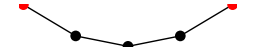

```mathematica
gr01=Graphics[{PointSize@.03,Line[{p1,p2,p3,p4,p5}],{Red,Point[{p1,p5}]},{Black,Point[{p2,p3,p4}]}},ImageSize->256]/.solution
```

```mathematica
fixedSupport=First@Cases[gr01,{Red,a_}:>First@a,All]
```

{{1,0},{5,0}}

```mathematica
points=First@Cases[gr01,{Black,a_}:>First@a,All]
```

{{2,-0.6},{3,-0.8},{4,-0.6}}

```mathematica
lines=First@Cases[gr01,a_Line:>Partition[First@a,2,1],All]
lengths=Counts[EuclideanDistance@@@lines]
```

{{{1,0},{2,-0.6}},{{2,-0.6},{3,-0.8}},{{3,-0.8},{4,-0.6}},{{4,-0.6},{5,0}}}

<|1.16619→2,1.0198→2|>

## 3D

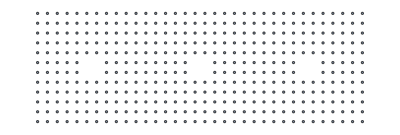

```mathematica
nx=34;ny=12;
Remove@#&/@{x,y,z};
vl1=Range[nx ny];
xy1=Tuples[{Range@nx,Range@ny}];

del=Reverse@Sort@Flatten[# 132+{66,67,78,79}&/@{0,1,2}];
xy=Delete[xy1,List/@del];
vl=Range@Length@xy;

Graph[vl,{},VertexCoordinates->xy,VertexLabels->None]
```

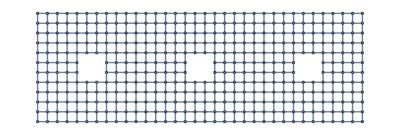

```mathematica
el=DeleteDuplicates[UndirectedEdge@@@(Sort/@Position[DistanceMatrix[xy],a_/;(a==1),2])];
Graph[vl,el[[1;;-1]],VertexCoordinates->xy,VertexLabels->None]
```

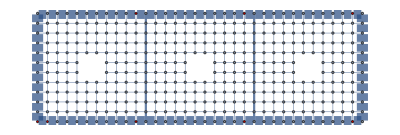

```mathematica
(*internal forces*)ew=.5&/@Range@Length@el;

(ew[[#]]=2)&/@Flatten[Position[el,#]&/@UndirectedEdge@@@Sort@Partition[#,2,1]]&@Flatten@Position[xy,{12|23,_},All];

(ew[[#]]=10)&/@Flatten[Position[el,#]&/@UndirectedEdge@@@Sort@Partition[#,2,1]]&@Flatten@Position[xy,{1|34,_},All];

(ew[[#]]=10)&/@Flatten[Position[el,#]&/@UndirectedEdge@@@Sort@Partition[#,2,1]]&@Flatten@Position[xy,{_,12},All];

(ew[[#]]=10)&/@Flatten[Position[el,#]&/@UndirectedEdge@@@Sort@Partition[#,2,1]]&@Flatten@Position[xy,{_,1},All];

(*set the boundaries*)
vc=MapIndexed[{x[First@#2],y[First@#2],z[First@#2]}&,xy];
fixed={1,13,117,128,245,256,373,384};
(x[#]=xy[[#,1]];y[#]=xy[[#,2]];z[#]=0;)&/@fixed;

graph=Graph[vl,el,VertexCoordinates->xy,VertexLabels->None,EdgeWeight->ew,EdgeStyle->Rule@@@Transpose[{el,(Thickness[#/500]&/@ew)}],VertexStyle->((#->Red)&/@fixed)]
```

```mathematica
(*the internal set of linear equations*)sys=Function[n,Simplify@Total[(ew[[First@Flatten@Position[el,UndirectedEdge@@Sort@{#,n}]]](vc[[#]]-vc[[n]]))&/@AdjacencyList[graph,n]]]/@DeleteDuplicates@Cases[vc,_[a_]:>a,All];
```

```mathematica
sys[[100]]
```

{0.5 x[90]+0.5 x[101]-2. x[102]+0.5 x[103]+0.5 x[114],0.5 y[90]+0.5 y[101]-2. y[102]+0.5 y[103]+0.5 y[114],0.5 z[90]+0.5 z[101]-2. z[102]+0.5 z[103]+0.5 z[114]}

```mathematica
env={0,.1,-.15}&/@sys;
```

```mathematica
rules=Solve[Equal@@@Transpose@{sys,env},Cases[vc,_[_],All]];
```

```mathematica
ef[pts_List,e_]:={Black,Line[pts]};
vf[pt_,name_,sz_]:={Black,Point[pt]};

gr02=Graph[vl,el,VertexCoordinates->Flatten[vc/. rules,1],EdgeShapeFunction->ef,VertexShapeFunction->vf]
```

-Graphics3D-

## AI

### Regression

```mathematica
data={#,RandomReal[{1.8,2.8}]+.3 #}&/@RandomReal[10,20]
```

{{9.9373,5.04867},{0.527705,2.3681},{8.71538,4.96659},{3.10856,2.87354},{5.19953,4.19511},{0.859694,3.01702},{0.883753,2.53984},{0.453698,2.34809},{8.92373,4.55412},{0.884473,2.72452},{7.29023,4.2727},{8.06521,5.10731},{2.3042,3.42283},{4.33454,3.94167},{0.951782,2.15917},{3.85511,3.28243},{6.90907,4.29239},{6.60972,4.43519},{7.02041,4.22931},{2.88402,3.25196}}

2.36621+0.286523 x

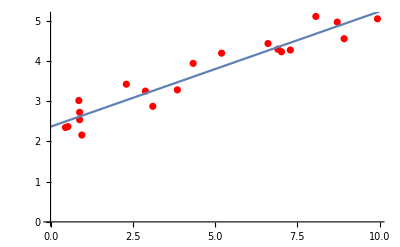

```mathematica
n=1;
line=Fit[data,x^#&/@Range[0,n],x]
Show[ListPlot[data,PlotStyle->Red],Plot[{line},{x,0,10}]]
```

1.68085+1.84234 x-1.15905 x^2+0.391894 x^3-0.0652075 x^4+0.00521876 x^5-0.00016089 x^6

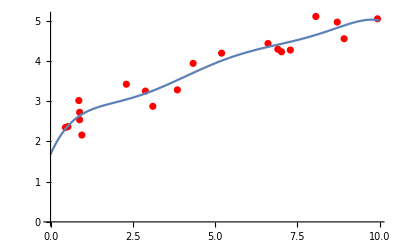

```mathematica
n=6;
line=Fit[data,x^#&/@Range[0,n],x]
Show[ListPlot[data,PlotStyle->Red],Plot[{line},{x,0,10}]]
```

### Classify

```mathematica
trainingSet={

};
```

```mathematica
cf1=Classify[trainingSet]
```

ClassifierFunction[…]

```mathematica
cf1["architect"]
```

student